```mathematica
da= 1/2 {{0.05, 0.1}, {0.05,-0.1},{-0.05, -0.1},{-0.05,0.1}}
```

{{0.025,0.05},{0.025,-0.05},{-0.025,-0.05},{-0.025,0.05}}

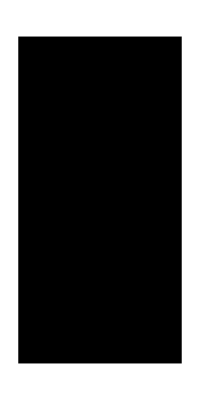

```mathematica
Polygon[%]//Graphics
```

```mathematica
dat=Composition[TranslationTransform[{0.15,0}],RotationTransform[ Pi/4],TranslationTransform[{0.05,0}]][da]
```

{{0.167678,0.0883883},{0.238388,0.0176777},{0.203033,-0.0176777},{0.132322,0.053033}}

```mathematica
dbt=Composition[TranslationTransform[{0.15,0}],RotationTransform[ Pi/4],TranslationTransform[{-0.05,0}]][da]
```

{{0.096967,0.0176777},{0.167678,-0.053033},{0.132322,-0.0883883},{0.0616117,-0.0176777}}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pbialas/PET/tools/src/2d/geometry

```mathematica
Export["gate_volume_test.txt", Join[dat, dbt], "Table"]
```

gate_volume_test.txt

```mathematica
LinearRepeat[poly_, ltr_, n_, v_]:= Module[{last = (n-1) v},
Composition[TranslationTransform[#],ltr][poly]&/@Table[v*i-last/2,{i,0,n-1}]
]
```

```mathematica
pr=LinearRepeat[da,TranslationTransform[{0,0}],4 , {0.1, 0.0}]
```

{{{-0.125,0.05},{-0.125,-0.05},{-0.175,-0.05},{-0.175,0.05}},{{-0.025,0.05},{-0.025,-0.05},{-0.075,-0.05},{-0.075,0.05}},{{0.075,0.05},{0.075,-0.05},{0.025,-0.05},{0.025,0.05}},{{0.175,0.05},{0.175,-0.05},{0.125,-0.05},{0.125,0.05}}}

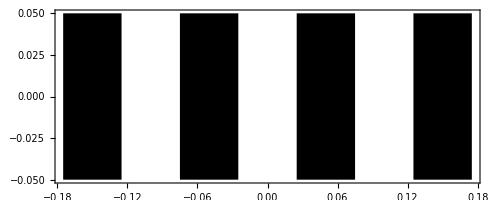

```mathematica
Graphics[Polygon/@pr, Frame->True]
```

```mathematica
Export["gate_volume_s_repeater_test.txt",Flatten[pr,1],"Table"]
```

gate_volume_s_repeater_test.txt

```mathematica
RingRepeat[poly_, ltr_, n_, angle_, center_: {0,0}]:= Module[{last = (n-1) v, t},
Composition[RotationTransform[#, center],ltr][poly]&/@Table[angle/n *i ,{i,0,n-1}]
]
```

```mathematica
rr=RingRepeat[da,TranslationTransform[{0,0.2}],4,2 Pi, {0.0, 0.0}]
```

{{{0.025,0.25},{0.025,0.15},{-0.025,0.15},{-0.025,0.25}},{{-0.25,0.025},{-0.15,0.025},{-0.15,-0.025},{-0.25,-0.025}},{{-0.025,-0.25},{-0.025,-0.15},{0.025,-0.15},{0.025,-0.25}},{{0.25,-0.025},{0.15,-0.025},{0.15,0.025},{0.25,0.025}}}

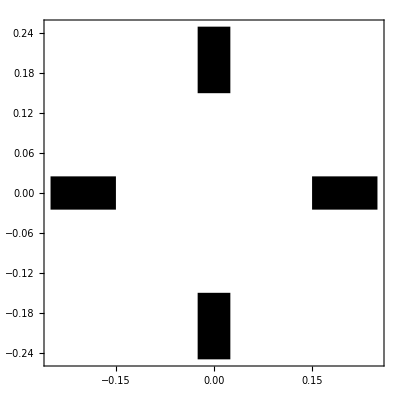

```mathematica
Graphics[Polygon/@rr, Frame->True]
```